## Adiabatic Bouncer model

-Graphics-
with
-Graphics-

## Find Directory

```mathematica
NOME=NotebookDirectory[]; (* Find directory where this notebook is placed *)
```

```mathematica
SetDirectory[NOME];
```

```mathematica
SetDirectory[StringJoin[NOME,"DadosVrms"]] ;
```

## REading Root mean square of velocities as function of ζ and z

```mathematica
Clear[data];(*LaunchKernels[kernel];*)
```

```mathematica
data={};Do[Zet=StringJoin[DeleteCases[StringSplit[ToString[ζ],""],"."]];fileNames=StringJoin["Vrms-",Zet,".txt"];AppendTo[data,Quiet[ToExpression[Import[fileNames]][[1]]]],{ζ,0.2,5,0.1}];
```

```mathematica
LZeta=Length[data]
```

49

```mathematica
LZ=Length[data[[1]]]
```

101

```mathematica
dataF=data;
```

```mathematica
pos={};Do[If[dataF[[ζ]][[z]][[3]][[600]]<10^-5,dataF[[ζ]][[z]][[3]]=0.0,AppendTo[pos,{ζ,z}]],{z,1,LZ},{ζ,1,LZeta}]
```

```mathematica
Do[dataF[[pos[[i,1]]]][[pos[[i,2]]]][[3]]=dataF[[pos[[i,1]]]][[pos[[i,2]]]][[3]]/dataF[[pos[[i,1]]]][[pos[[i,2]]]][[3]][[1]],{i,1,Length[pos]}];
```

```mathematica
Do[Do[dataF[[pos[[i,1]]]][[pos[[i,2]]]][[3]][[j]]={j 1000,dataF[[pos[[i,1]]]][[pos[[i,2]]]][[3]][[j]]},{j,1,600}],{i,1,Length[pos]}];
```

```mathematica
Length[pos]
```

2753

```mathematica
FindFit[dataF[[49,71]][[3]][[300;;600]],a n^b,{a,b},n]
```

{a→0.00841658,b→0.635259}

```mathematica
diff=Quiet[Table[b/.FindFit[dataF[[pos[[i,1]]]][[pos[[i,2]]]][[3]][[300;;600]],a x^b,{a,b},x],{i,1,Length[pos]}]];
```

```mathematica
Do[If[diff[[i]]<0,diff[[i]]=0.],{i,1,Length[diff]}]
```

```mathematica
Do[dataF[[pos[[i,1]]]][[pos[[i,2]]]][[3]]=diff[[i]],{i,1,Length[pos]}];
```

```mathematica
dataT=dataF[[1]];Do[dataT=Union[dataT,dataF[[i]]],{i,2,Length[dataF]}];
```

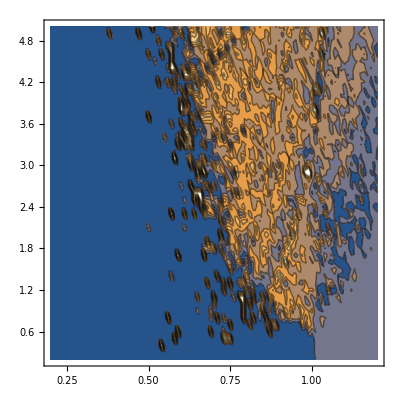

```mathematica
ListContourPlot[dataT]
```

```mathematica
dataTClass=dataT;Do[If[dataTClass[[i]][[3]]<0.08,dataTClass[[i]][[3]]=0.0];If[0.485≤dataTClass[[i]][[3]]≤0.515,dataTClass[[i]][[3]]=0.5];If[0.08≤dataTClass[[i]][[3]]<0.485,dataTClass[[i]][[3]]=0.3];If[0.515<dataTClass[[i]][[3]],dataTClass[[i]][[3]]=0.7],{i,1,Length[dataTClass]}]
```

```mathematica
f=Interpolation[dataTClass];
```

```mathematica
fig1A=ContourPlot[f[x,y],{x,0.2,1.2},{y,0.2,5},ColorFunction->"GrayTones",Contours->{0.01,0.495,0.505},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->200,LegendFunction->"Frame",LegendLabel->"Diffusivity",LabelStyle->{FontSize->15,Black}],{After,Center}],Frame->True,FrameStyle->Directive[Black,FontSize->17],FrameLabel->{Style["z",FontSize->17,Black],Style["ζ",FontSize->17,Black]},AspectRatio->2/4,ImageSize->500]
```

-Graphics-

```mathematica
fig1A=With[{min=0,max=0.7},ContourPlot[f[x,y],{x,0.2,1.2},{y,0.2,5},ColorFunctionScaling->False,ColorFunction->(ColorData[{"DarkRainbow",{min,max}}]),Contours->{0.01,0.495,0.505},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->200,LegendFunction->"Frame",LegendLabel->"Diffusivity",LabelStyle->{FontSize->15,Black}],{After,Center}],Frame->True,FrameStyle->Directive[Black,FontSize->16],FrameLabel->{Style["z",FontSize->17,Black],Style["ζ",FontSize->17,Black]},AspectRatio->2/4,ImageSize->610]]
```

-Graphics-

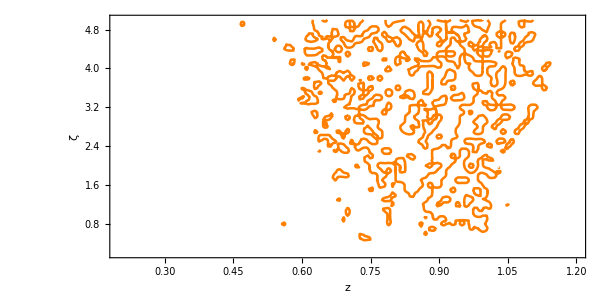

```mathematica
fig1C=ContourPlot[f[x,y]==0.5,{x,0.2,1.2},{y,0.2,5},Frame->True,ContourStyle->Directive[Orange,Thickness[0.003]],FrameStyle->Directive[Black,FontSize->16],FrameLabel->{Style["z",FontSize->17,Black],Style["ζ",FontSize->17,Black]},AspectRatio->2/4,ImageSize->610]
```

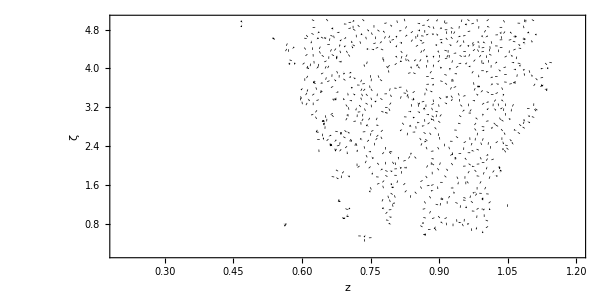

```mathematica
fig1D=ContourPlot[f[x,y]==0.5,{x,0.2,1.2},{y,0.2,5},Frame->True,ContourStyle->Directive[Black,Dotted,Thickness[0.003]],FrameStyle->Directive[Black,FontSize->16],FrameLabel->{Style["z",FontSize->17,Black],Style["ζ",FontSize->17,Black]},AspectRatio->2/4,ImageSize->610]
```

```mathematica
Show[{fig1A,fig1C,fig1D}]
```

-Graphics-

```mathematica
front=Cases[Normal@fig1C,Line[x_]:>x,Infinity];
```

```mathematica
points={};Do[points=Union[points,front[[i]]],{i,1,Length[front]}];
```

```mathematica
Length[points]
```

5612

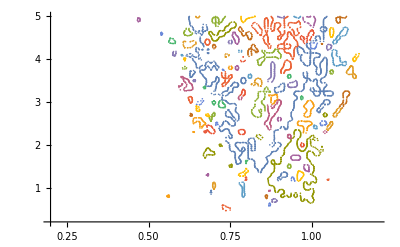

```mathematica
ListPlot[front,PlotRange->{{0.2,1.2},{0.2,5}}]
```

## Test on fractal dimension

```mathematica
(*Box-Counting function*)boxCount[points_,boxSize_]:=Module[{grid,counts},(*Translate points to positive coordinates*)grid=Floor[points/boxSize];
(*Count unique grid points*)Length[Union[grid]]];
```

```mathematica
(*Define a range of box sizes*)boxSizes=N[Range[0.01,0.5,0.01]];
```

```mathematica
(*Apply the Box-Counting method*)
counts=Table[boxCount[points,size],{size,boxSizes}];
```

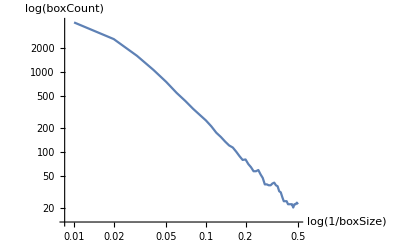

```mathematica
(*Log-log plot of box counts vs.box sizes*)ListLogLogPlot[Transpose[{boxSizes,counts}],Joined->True,AxesLabel->{"log(1/boxSize)","log(boxCount)"}]
```

```mathematica
(*Linear fit to estimate the fractal dimension*)
fit=LinearModelFit[Log[{1/boxSizes,counts}]//Transpose,x,x];
Df=fit["BestFitParameters"]
```

{1.90668,1.51742}

## Theoretical approach

```mathematica
NSolve[Log[η]/Log[0.001]==0.81,η]
```

{{η→0.00371535}}

```mathematica
z[ζ_]:=0.81+Log[ζ]/Log[0.001]
```

```mathematica
0.86+Log[ζ]/Log[0.01]
```

0.86-0.217147 Log[ζ]

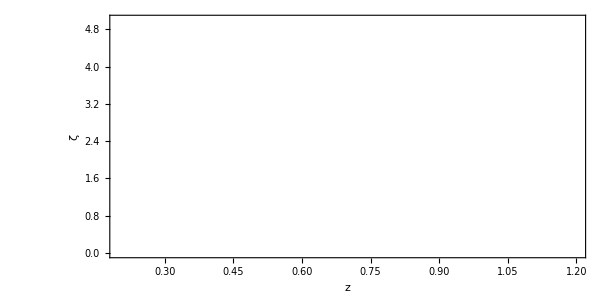

```mathematica
figTeo=ParametricPlot[{z[ζ],ζ},{ζ,0.2,6},PlotRange->{{0.2,1.2},{0,5}},PlotStyle->Directive[White,Thickness[0.003]],PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->200,LegendFunction->"Frame",LegendLabel->"Diffusivity",LabelStyle->{FontSize->15,Black}],{After,Center}],Frame->True,FrameStyle->Directive[Black,FontSize->16],FrameLabel->{Style["z",FontSize->17,Black],Style["ζ",FontSize->17,Black]},AspectRatio->2/4,ImageSize->610]
```

```mathematica
Show[{fig1A,fig1C,fig1D,figTeo}]
```

-Graphics-